## Definition

## Definition

## Definition

```mathematica
ClearAll[FindRandomMazeSolution]
```

#### Main Definition

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[{m1,n1}],property]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[{m1,n1}],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### specify start and end

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_]:=Module[{g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_,property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})|ContainsOnly[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"}][property]]]:=Lookup[FindRandomMazeSolution[{m1,n1},start,end],property]
```

#### an antipodal maze

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Antipodal"]:=Module[{g,maze,highlightedStartEnd,m,solvedmaze,shortestPath,shortestPathSubgraph,start,end},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
{start,end}=ResourceFunction["GraphAntipodes"][m];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];highlightedStartEnd=HighlightGraph[maze,{start,end}];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->highlightedStartEnd,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Antipodal",property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})|ContainsOnly[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"}][property]]]:=Lookup[FindRandomMazeSolution[{m1,n1},"Antipodal"],property]
```

#### Triangular Main Definition

```mathematica
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular"]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=ResourceFunction["TriangularGridGraph"][m1];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=Last[VertexList[g]];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})|ContainsOnly[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"}][property]]]:=Lookup[FindRandomMazeSolution[m1,"Triangular"],property]
```

#### Hexagonal Main Definition

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Hexagonal"]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=ResourceFunction["HexagonalGridGraph"][{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=Last[VertexList[g]];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
```

## Hexagonal Graph

```mathematica
MatchQ[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property_/;MatchQ[property,(ContainsOnly[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"}][property])]]
```

False

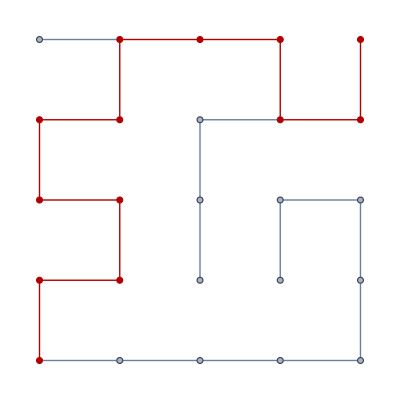
<|shortest-path→{1,2,3,4,5,10,15,20,25},solved-maze→-Graphics-|>

```mathematica
FindRandomMazeSolution[{5,5},{"solved-maze","shortest-path"}]
```

```mathematica
AssessmentFunction[{{1,2,3,4,5,10,15,20,25}}][{1,2,3,4,5,10,15,20,25}]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{{1,2,3,4,5,10,15,20,25}}][{1,2,3,4,5,10,15,20,25}]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1}][1]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1}][2]
```

AssessmentResultObject[…]